# EIWL Sections 18 and 19 - Harper Yonago

### Section 18

```mathematica
GeoDistance[,]
```

3453.71 mi

```mathematica
GeoDistance[,]/GeoDistance[,]
```

1.35109

```mathematica
UnitConvert[GeoDistance[,],"Kilometers"]
```

14387. km

```mathematica
GeoGraphics[]
```

-Graphics-

```mathematica
GeoListPlot[{,,,}]
```

-Graphics-

```mathematica
GeoGraphics[GeoPath[{Entity["City",{"NewYork","NewYork","UnitedStates"}],Entity["City",{"Beijing","Beijing","China"}]}]]
```

GeoServer::vtiles: Unable to download one or more vector tiles.

-Graphics-

```mathematica
GeoGraphics[GeoDisk[,]]
```

-Graphics-

```mathematica
GeoGraphics[GeoDisk[Entity["City",{"NewYork","NewYork","UnitedStates"}],GeoDistance[Entity["City",{"NewYork","NewYork","UnitedStates"}],Entity["City",{"SanFrancisco","California","UnitedStates"}]]]]
```

GeoServer::vtiles: Unable to download one or more vector tiles.

-Graphics-

```mathematica
GeoImage[GeoDisk[Entity["Building","ThePentagon::qzh8d"],Quantity[0.4, "Miles"]]]
```

-Graphics-

```mathematica
GeoNearest["Country",GeoPosition["NorthPole"],5]
```

{Greenland,Canada,Russia,Svalbard,United States}


{-Graphics-,-Graphics-,-Graphics-}

```mathematica
EntityValue[GeoNearest["Country",GeoPosition[{45,0}],3],"Flag"]
```

```mathematica
GeoListPlot[GeoNearest["Volcano",,25]]
```

-Graphics-

```mathematica
(GeoPosition[][[1]][[1]])-(GeoPosition[][[1]][[1]])
```

6.64488

### Section 19

```mathematica
Now-
```

45695. days

```mathematica
DayName[]
```

Saturday

```mathematica
Now- Quantity[100000, "Days"]
```

Tue 27 Apr 1751 19:55:22GMT-7

```mathematica
LocalTime[Entity["City",{"Delhi","Delhi","India"}]]
```

Mon 10 Feb 2025 08:25:22GMT+5.5

```mathematica
Sunset[Here, Today]-Sunrise[Here,Today]
```

10.8187 h

```mathematica
MoonPhase[DateObject[{2025,2,9},"Day"],"Icon"]
```

-Graphics-

```mathematica
Table[MoonPhase[Today+x Quantity[, "Days"]],{x,1,10}]
```

{0.943238,0.981443,0.998399,0.994506,0.971049,0.929957,0.87353,0.804225,0.7245,0.636771}

```mathematica
Table[MoonPhase[Today+x Quantity[, "Days"],"Icon"],{x,1,10}]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Sunrise[Entity["City",{"London","GreaterLondon","UnitedKingdom"}],Today]-Sunrise[Entity["City",{"NewYork","NewYork","UnitedStates"}],Today]
```

-4.52766 h

```mathematica
UnitConvert[Now-DateObject[Entity["MannedSpaceMission","Apollo11"][EntityProperty["MannedSpaceMission","LunarLandingDate"]]],"Years"]
```

55.598 yr

```mathematica
AirTemperatureData[Entity["Building","EiffelTower::5h9w8"],]
```

42.8 °F

```mathematica
Table[AirTemperatureData[,Today-x Quantity[, "Days"]],{x,1,10}]
```

{(39.2to44.6) °F,(35.6to44.6) °F,(35.6to41.) °F,(33.8to42.8) °F,(30.2to37.4) °F,(28.4to46.4) °F,(26.6to44.6) °F,(30.2to44.6) °F,(32.to44.6) °F,(35.6to46.4) °F}

```mathematica
AirTemperatureData[,Now]-AirTemperatureData[,Now]
```

21.9 _Δ^◦F

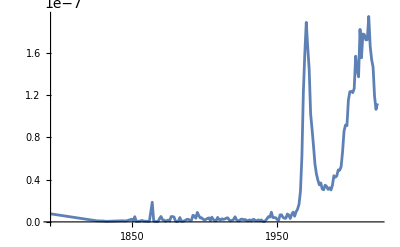

```mathematica
ListLinePlot[WordFrequencyData["groovy","TimeSeries"]]
```

```mathematica
[Dated["Population",2000]]-[Dated["Population",1900]]
```

20759628 people